```mathematica
(*********************************)
(*Dynamics of A Planar Mechanism*)
(*********************************)
SetOptions[EvaluationNotebook[],CellContext->Notebook]
```

```mathematica
(*Defining Absolute Coordinates*)
Do[(Subscript[r, j] = {Subscript[x, j][t],Subscript[y, j][t]}),{j,4}]
q=Join[Subscript[r, 1],{Subscript[θ, 1][t]},Subscript[r, 2],{Subscript[θ, 2][t]},Subscript[r, 3],{Subscript[θ, 3][t]},Subscript[r, 4],{Subscript[θ, 4][t]}]
```

{x_1[t],y_1[t],θ_1[t],x_2[t],y_2[t],θ_2[t],x_3[t],y_3[t],θ_3[t],x_4[t],y_4[t],θ_4[t]}

```mathematica
(*Defining Constraints*)
Φ = {Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[θ, 2][t],Subscript[x, 2][t]-Subscript[x, 1][t]+Subscript[y, 2][t]-Subscript[y, 1][t], Subscript[θ, 2][t]-Subscript[θ, 1][t],Subscript[x, 1][t]-Subscript[x, 3][t],Subscript[y, 1][t]-Subscript[y, 3][t],Subscript[x, 2][t]-Subscript[x, 4][t],Subscript[y, 2][t]-Subscript[y, 4][t], Subscript[x, 3][t]-Sin[Subscript[θ, 3][t]]-Subscript[x, 4][t]-Cos[Subscript[θ, 4][t]], Subscript[y, 3][t]+Cos[Subscript[θ, 3][t]]-Subscript[y, 4][t]-Sin[Subscript[θ, 4][t]]}
```

{y_1[t],θ_1[t],x_2[t],θ_2[t],-x_1[t]+x_2[t]-y_1[t]+y_2[t],-θ_1[t]+θ_2[t],x_1[t]-x_3[t],y_1[t]-y_3[t],x_2[t]-x_4[t],y_2[t]-y_4[t],-Cos[θ_4[t]]-Sin[θ_3[t]]+x_3[t]-x_4[t],Cos[θ_3[t]]-Sin[θ_4[t]]+y_3[t]-y_4[t]}

```mathematica
MatrixForm[%]
```

(y_1[t]
θ_1[t]
x_2[t]
θ_2[t]
-x_1[t]+x_2[t]-y_1[t]+y_2[t]
-θ_1[t]+θ_2[t]
x_1[t]-x_3[t]
y_1[t]-y_3[t]
x_2[t]-x_4[t]
y_2[t]-y_4[t]
-Cos[θ_4[t]]-Sin[θ_3[t]]+x_3[t]-x_4[t]
Cos[θ_3[t]]-Sin[θ_4[t]]+y_3[t]-y_4[t])

```mathematica
J= D[Φ,{q}] (* Jacobian Matrix *)
```

{{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{-1,-1,0,1,1,0,0,0,0,0,0,0},{0,0,-1,0,0,1,0,0,0,0,0,0},{1,0,0,0,0,0,-1,0,0,0,0,0},{0,1,0,0,0,0,0,-1,0,0,0,0},{0,0,0,1,0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0,0,0,-1,0},{0,0,0,0,0,0,1,0,-Cos[θ_3[t]],-1,0,Sin[θ_4[t]]},{0,0,0,0,0,0,0,1,-Sin[θ_3[t]],0,-1,-Cos[θ_4[t]]}}

```mathematica
q' = D[q, t]
```

{x_1'[t],y_1'[t],θ_1'[t],x_2'[t],y_2'[t],θ_2'[t],x_3'[t],y_3'[t],θ_3'[t],x_4'[t],y_4'[t],θ_4'[t]}

```mathematica
Subscript[l, 1]=Subscript[l, 2]=1/2;
Subscript[l, 3]=Subscript[l, 4]=1;
m = 1;
(*Subscript[θ, 3]=Subscript[θ, 4]=0;*)
```

```mathematica
Subscript[M, 1]={{m,0,0},{0,m,0},{0,0,(m Subscript[l, 1]^2)/12}}
Subscript[M, 2]={{m,0,0},{0,m,0},{0,0,(m Subscript[l, 2]^2)/12}}
Subscript[M, 3]={{m,0,1/2 (-m) Subscript[l, 3] Sin[Subscript[θ, 3][t]]},{0,m,1/2 m Subscript[l, 3] Cos[Subscript[θ, 3][t]]},{1/2 (-m) Subscript[l, 3] Sin[Subscript[θ, 3][t]],1/2 m Subscript[l, 3] Cos[Subscript[θ, 3][t]],(m Subscript[l, 3]^2)/3}}
Subscript[M, 4]={{m,0,1/2 (-m) Subscript[l, 4] Sin[Subscript[θ, 4][t]]},{0,m,1/2 m Subscript[l, 4] Cos[Subscript[θ, 4][t]]},{1/2 (-m) Subscript[l, 4] Sin[Subscript[θ, 4][t]],1/2 m Subscript[l, 4] Cos[Subscript[θ, 4][t]],(m Subscript[l, 4]^2)/3}}
```

{{1,0,0},{0,1,0},{0,0,1/48}}

{{1,0,0},{0,1,0},{0,0,1/48}}

{{1,0,-1/2 Sin[θ_3[t]]},{0,1,1/2 Cos[θ_3[t]]},{-1/2 Sin[θ_3[t]],1/2 Cos[θ_3[t]],1/3}}

{{1,0,-1/2 Sin[θ_4[t]]},{0,1,1/2 Cos[θ_4[t]]},{-1/2 Sin[θ_4[t]],1/2 Cos[θ_4[t]],1/3}}

```mathematica
M = ArrayFlatten[{{Subscript[M, 1],0, 0, 0},{0,Subscript[M, 2],0,0},{0,0,Subscript[M, 3],0},{0,0,0,Subscript[M, 4]}}]
```

{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1/48,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1/48,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,-1/2 Sin[θ_3[t]],0,0,0},{0,0,0,0,0,0,0,1,1/2 Cos[θ_3[t]],0,0,0},{0,0,0,0,0,0,-1/2 Sin[θ_3[t]],1/2 Cos[θ_3[t]],1/3,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,-1/2 Sin[θ_4[t]]},{0,0,0,0,0,0,0,0,0,0,1,1/2 Cos[θ_4[t]]},{0,0,0,0,0,0,0,0,0,-1/2 Sin[θ_4[t]],1/2 Cos[θ_4[t]],1/3}}

```mathematica
MatrixRank[J]
```

11

```mathematica
(*RowReduce[J] //MatrixForm*)
```

```mathematica
J = Drop[J,{2},0] (*Eliminating a dependent constraint, arbitrarily*)
(*J = J⟦{7,8,9,10,11,12},All⟧ *) (*Choosing only the constraints for which joint reactions can be solved for uniquely*)
```

{{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{-1,-1,0,1,1,0,0,0,0,0,0,0},{0,0,-1,0,0,1,0,0,0,0,0,0},{1,0,0,0,0,0,-1,0,0,0,0,0},{0,1,0,0,0,0,0,-1,0,0,0,0},{0,0,0,1,0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0,0,0,-1,0},{0,0,0,0,0,0,1,0,-Cos[θ_3[t]],-1,0,Sin[θ_4[t]]},{0,0,0,0,0,0,0,1,-Sin[θ_3[t]],0,-1,-Cos[θ_4[t]]}}

```mathematica
JIn = PseudoInverse[J]
```

{«1»}

```mathematica
Subscript[Q, e]= {1,0,0,0,0,0,0,0,0,0,0,0}
```

{1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
q' = D[q, t]
```

{x_1'[t],y_1'[t],θ_1'[t],x_2'[t],y_2'[t],θ_2'[t],x_3'[t],y_3'[t],θ_3'[t],x_4'[t],y_4'[t],θ_4'[t]}

```mathematica
Subscript[Q, d]=-(D[(J.q'), {q}]).q'
```

{0,0,0,0,0,0,0,0,0,-Sin[θ_3[t]] θ_3'[t]^2-Cos[θ_4[t]] θ_4'[t]^2,Cos[θ_3[t]] θ_3'[t]^2-Sin[θ_4[t]] θ_4'[t]^2}

```mathematica
MIn = Inverse[M]
```

{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,48,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,48,0,0,0,0,0,0},{0,0,0,0,0,0,(1/3-1/4 Cos[θ_3[t]]^2)/(1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2),-(Cos[θ_3[t]] Sin[θ_3[t]])/(4 (1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2)),Sin[θ_3[t]]/(2 (1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2)),0,0,0},{0,0,0,0,0,0,-(Cos[θ_3[t]] Sin[θ_3[t]])/(4 (1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2)),(1/3-1/4 Sin[θ_3[t]]^2)/(1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2),-Cos[θ_3[t]]/(2 (1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2)),0,0,0},{0,0,0,0,0,0,Sin[θ_3[t]]/(2 (1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2)),-Cos[θ_3[t]]/(2 (1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2)),1/(1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2),0,0,0},{0,0,0,0,0,0,0,0,0,(1/3-1/4 Cos[θ_4[t]]^2)/(1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2),-(Cos[θ_4[t]] Sin[θ_4[t]])/(4 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2)),Sin[θ_4[t]]/(2 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2))},{0,0,0,0,0,0,0,0,0,-(Cos[θ_4[t]] Sin[θ_4[t]])/(4 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2)),(1/3-1/4 Sin[θ_4[t]]^2)/(1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2),-Cos[θ_4[t]]/(2 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2))},{0,0,0,0,0,0,0,0,0,Sin[θ_4[t]]/(2 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2)),-Cos[θ_4[t]]/(2 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2)),1/(1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2)}}

```mathematica
Jt = Transpose[J]
```

{{0,0,0,-1,0,1,0,0,0,0,0},{1,0,0,-1,0,0,1,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0},{0,1,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,1,0},{0,0,0,0,0,0,-1,0,0,0,1},{0,0,0,0,0,0,0,0,0,-Cos[θ_3[t]],-Sin[θ_3[t]]},{0,0,0,0,0,0,0,-1,0,-1,0},{0,0,0,0,0,0,0,0,-1,0,-1},{0,0,0,0,0,0,0,0,0,Sin[θ_4[t]],-Cos[θ_4[t]]}}

```mathematica
JMinJt = Inverse[J.MIn.Jt]
```

{{1/(«1»)(-(-(Cos[θ_3[t]] Sin[θ_3[t]])/(4 (1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2))-Sin[θ_3[t]]^2/(2 (1/3-1/4 Cos[«1»]^2-1/4 Sin[θ_3[t]]^2))-Cos[θ_3[t]] (-Cos[θ_3[t]]/(2 (1/3-«1» «1»-1/4 («1»)^2))-Sin[«1»]/(1/3-«1»«1»«1»))-(Cos[θ_4[t]] Sin[θ_4[t]])/(4 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2))) («1»)+«43»+«1»),(-(Cos[θ_4[t]] Sin[θ_4[t]] («1»))/(4 (1/3-1/4 Cos[«1»]^2-1/4 Sin[θ_4[t]]^2))+«24»+(-Cos[«1»]^2/(2 (1/3-«1»-1/4 «1»))+(«1»-«1»)/(«1»)) («1»))/(«1»),0,(-(-(«1»)^2/(2 («1»))+(1/3-«1»)/(1/3-«1»«1»«1»)) («1»)+«23»)/(«1»),0,(«1»)/(«1»),(«1»)/(«1»),(«1»)/(«1»),(«53»+(«1»)/(«1»))/(«1»),(«1»)/(«1»),(«1»)/(«1»)},«9»,{(«1»)/(«1»),(«1»)/(«1»),«8»,(«1»)/(«1»)}}

```mathematica
(*q''=MIn.Subscript[Q, e]+MIn.Jt.(JMinJt.(Subscript[Q, d]-J.MIn.Subscript[Q, e]))*)
```

```mathematica
eqs = D[D[q, t], t] - (MIn.Subscript[Q, e]+MIn.Jt.(JMinJt.(Subscript[Q, d]-J.MIn.Subscript[Q, e]))) == {0,0,0,0,0,0,0,0,0,0,0,0}
(*eqns1 = ∂_t ∂_t q - (MIn.Subscript[Q, e]+MIn.Jt.(JMinJt.(Subscript[Q, d]-J.MIn.Subscript[Q, e])))*)
```

{-1+(«1»)/(«1»)-((Cos[θ_4[t]] Sin[θ_4[t]] (-(«1»)/(24 («1») («1»)^2)+(«1»)/(«1»)+«6»))/(4 (1/3-1/4 Cos[«1»]^2-1/4 Sin[θ_4[t]]^2))+«43»)/(«1»)-((-(«1»)^2/(6 («1»)^2)+«17») (-(«1»)^2/(2 «1»)+(«1»)/(«1»))+«40»)/(«1»)+(«1»)/(«1»)+((«1») («1»))/(«1»)-((«1») («1»))/(«1»)+((«1») (Cos[θ_3[t]] θ_3'[t]^2-Sin[θ_4[t]] («1»'[t])^2))/(«1»)-(((Cos[θ_3[t]] Cos[θ_4[t]]^2 Sin[θ_3[t]] Sin[θ_4[t]]^2)/(64 (1/3-1/4 Cos[θ_3[t]]^2-1/4 Sin[θ_3[t]]^2) (1/3-1/4 Cos[«1»]^2-1/4 Sin[θ_4[t]]^2)^2)-(Cos[θ_4[t]] «1» («1»))/(4 (1/3-«1»-1/4 («1»)^2))+«67»+(Cos[θ_4[t]] Sin[θ_4[t]] («1»))/(4 (1/3-1/4 Cos[«1»]^2-1/4 Sin[θ_4[t]]^2))) («1»))/(«1»)+x_1''[t],«19»+«1»,«8»,«1»,«1»}=={«1»}

```mathematica
(*λ = JMinJt.(Subscript[Q, d]-J.MIn.Subscript[Q, e])*)
(*Subscript[Q, c] = {Subscript[Q, 1][t],Subscript[Q, 2][t],Subscript[Q, 3][t],Subscript[Q, 4][t],Subscript[Q, 5][t],Subscript[Q, 6][t],Subscript[Q, 7][t],Subscript[Q, 8][t],Subscript[Q, 9][t],Subscript[Q, 10][t],Subscript[Q, 11][t],Subscript[Q, 12][t]}
eqns2 = Subscript[Q, c] -Jt.JMInJt.(Subscript[Q, d]-J.MIn.Subscript[Q, e])*)
(*eqns2 = Subscript[Q, c]- (Subscript[Q, e]- M.Inverse[J].Subscript[Q, d])*)
```

```mathematica
(*eqns=Join[eqns1,eqns2]=={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}*)
```

```mathematica
s=NDSolve[{eqs,Subscript[x, 1][0]==1,Subscript[y, 1][0]==0,Subscript[θ, 1][0]==0,Subscript[x, 1]'[0]==0,Subscript[y, 1]'[0]==0,Subscript[θ, 1]'[0]==0,Subscript[x, 2][0]==0,Subscript[y, 2][0]==1,Subscript[θ, 2][0]==0,Subscript[x, 2]'[0]==0,Subscript[y, 2]'[0]==0,Subscript[θ, 2]'[0]==0, Subscript[x, 3][0]==1,Subscript[y, 3][0]==0,Subscript[θ, 3][0]==0,Subscript[x, 3]'[0]==0,Subscript[y, 3]'[0]==0,Subscript[θ, 3]'[0]==0, Subscript[x, 4][0]==0,Subscript[y, 4][0]==1,Subscript[θ, 4][0]==0,Subscript[x, 4]'[0]==0,Subscript[y, 4]'[0]==0,Subscript[θ, 4]'[0]==0},{Subscript[x, 1],Subscript[y, 1],Subscript[θ, 1],Subscript[x, 2],Subscript[y, 2],Subscript[θ, 2],Subscript[x, 3],Subscript[y, 3],Subscript[θ, 3],Subscript[x, 4],Subscript[y, 4],Subscript[θ, 4],Subscript[x, 1]',Subscript[y, 1]',Subscript[θ, 1]',Subscript[x, 2]',Subscript[y, 2]',Subscript[θ, 2]',Subscript[x, 3]',Subscript[y, 3]',Subscript[θ, 3]',Subscript[x, 4]',Subscript[y, 4]',Subscript[θ, 4]'},{t,0,5}, Method->{"EquationSimplification"->"Solve"}]
```

{{x_1→InterpolatingFunction[{{0.,5.}},<>],y_1→InterpolatingFunction[{{0.,5.}},<>],θ_1→InterpolatingFunction[{{0.,5.}},<>],x_2→InterpolatingFunction[{{0.,5.}},<>],y_2→InterpolatingFunction[{{0.,5.}},<>],θ_2→InterpolatingFunction[{{0.,5.}},<>],x_3→InterpolatingFunction[{{0.,5.}},<>],y_3→InterpolatingFunction[{{0.,5.}},<>],θ_3→InterpolatingFunction[{{0.,5.}},<>],x_4→InterpolatingFunction[{{0.,5.}},<>],y_4→InterpolatingFunction[{{0.,5.}},<>],θ_4→InterpolatingFunction[{{0.,5.}},<>],x_1'→InterpolatingFunction[{{0.,5.}},<>],y_1'→InterpolatingFunction[{{0.,5.}},<>],θ_1'→InterpolatingFunction[{{0.,5.}},<>],x_2'→InterpolatingFunction[{{0.,5.}},<>],y_2'→InterpolatingFunction[{{0.,5.}},<>],θ_2'→InterpolatingFunction[{{0.,5.}},<>],x_3'→InterpolatingFunction[{{0.,5.}},<>],y_3'→InterpolatingFunction[{{0.,5.}},<>],θ_3'→InterpolatingFunction[{{0.,5.}},<>],x_4'→InterpolatingFunction[{{0.,5.}},<>],y_4'→InterpolatingFunction[{{0.,5.}},<>],θ_4'→InterpolatingFunction[{{0.,5.}},<>]}}

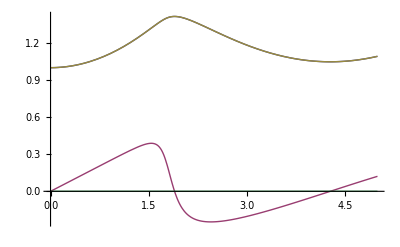

-Graphics-

```mathematica
Plot[Evaluate[{Subscript[x, 3][t],Subscript[x, 3]'[t] ,Subscript[y, 2][t],Subscript[θ, 1][t]}/.s],{t,0,5},PlotStyle->Automatic]
```

```mathematica
Subscript[θ, 3][2]/.s
J/.t->2/.s
λ = JMinJt.(Subscript[Q, d]-J.MIn.Subscript[Q, e])
```

{0.886271}

{{{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{-1,-1,0,1,1,0,0,0,0,0,0,0},{0,0,-1,0,0,1,0,0,0,0,0,0},{1,0,0,0,0,0,-1,0,0,0,0,0},{0,1,0,0,0,0,0,-1,0,0,0,0},{0,0,0,1,0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0,0,0,-1,0},{0,0,0,0,0,0,1,0,-0.632306,-1,0,-0.774719},{0,0,0,0,0,0,0,1,-0.774719,0,-1,-0.632306}}}

{(-(-Cos[θ_4[t]]^2/(2 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2))+(1/3-1/4 Sin[θ_4[t]]^2)/(1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2)) ((Cos[θ_4[t]] Sin[θ_4[t]] («32»+(«1»)/(«1»)))/(4 (1/3-1/4 Cos[θ_4[t]]^2-1/4 Sin[θ_4[t]]^2))-(Cos[«1»]^2/(9 («1»)^3)-(«1»)/(6 «1»)+«41»+((«1»)^2 («1»)^2)/(16 («1») («1»))) («1»))+«23»)/(«1»)-(-(«1») (-1/(9 («1»)^2)+(«1»)/(«1»)+(«1»)/(«1»)+(Cos[θ_3[t]] «2» Sin[θ_4[t]])/(16 («1») (1/3-1/4 («1»)^2-1/4 («1»)^2)))+«60»)/(«1»)+((«1») (-Sin[θ_3[t]] («1»'[t])^2-Cos[«1»[t]] «1»))/(«1»)+((«43»+(«1»)/(«1»)) (Cos[θ_3[t]] θ_3'[t]^2-Sin[θ_4[t]] θ_4'[t]^2))/(«1»),«1»,0,«6»,«1»,(«1»)/(«1»)-(«1»)/(«1»)+(«1»)/(«1»)+((«1») («1» «1»-«1»))/(«1»)}

```mathematica
λ/.t->1/.s
```

{{0.539284,-0.528874,0,0.352806,0,-0.377552,-0.186478,0.176067,-0.0831644,-0.141989,0.0421465}}

```mathematica
Dimensions[λ]
(*This should come out to be 11, and not 12*)
```

{11}

```mathematica
f = Jt.λ
Dimensions[f]
```

{«1»}

{12}

```mathematica
(*Table[Plot[Evaluate[λ[[j]]/.s],{t,0,5},PlotStyle->Automatic, AxesLabel->{Time,"Generalized Force"}, PlotLabel->Subscript[f, j+1]],{j,6,11}]*)
(* We are plotting reactions for only those joints for which the net joint reaction can be solved uniquely*)
(* I've done j+1 as label, because 2nd constraint was removed from Jacobian so constraints labels have shifted by 1 *)
```

```mathematica
Table[Plot[Evaluate[f[[j]]/.s,{t,0,5}, AccuracyGoal -> 20,PrecisionGoal -> 20],PlotStyle->Automatic, AxesLabel->{Time,"Generalized Force"}, PlotLabel->Subscript[f, j]],{j,7,12}]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.